# Bead in a Standing Wave

```mathematica
F[x,t] == m*x''[t]
```

```mathematica
F[x,t] = Fnot*Sin[x]*Sin[t];
```

```mathematica
A = Fnot/m;
```

```mathematica
Control[{A,0,20}]
```

Inertia is significant (high Reynold’s number).

{{x[t]→InterpolatingFunction[{{0.,30.}},<>][t]}}

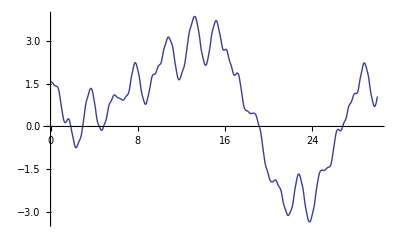

```mathematica
s=NDSolve[{x''[t] == A*Sin[2π*x[t]]*Sin[2π*t],x[0] == π/2, x'[0] == 0},x[t],{t,0,30}]
Plot[x[t]/.s,{t,0,30}]
```

Inertia is insignificant (low Reynold’s number).

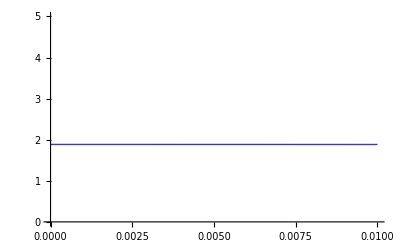

```mathematica
s=NDSolve[{x'[t] == A*Sin[2π*x[t]]*Sin[2π*t],x[0] == π(0.6)},x[t],{t,0,0.1}];
Plot[x[t]/.s,{t,0,0.01},PlotRange-> {0,5}]
```